## 計算結果

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]
json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_multiple/result.json"
(*json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_3/result.json"*)
json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.json"
(*json="/Volumes/home/BEM/20240301土木学会東北支部/Tanizawa1996_H0d05_L1d8_potential_multiple_water_mod_coarse/result.json"*)
(*json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential/result.json"*)
imported=Import[json];
getData[var_,n_:0]:=If[n>0,(var/.imported)[[;;,n]],var/.imported];
importGetData[name_,var_,n_:0]:=With[{imported=Import[name]},If[n>0,(var/.imported)[[;;,n]],var/.imported]];
importData[name_,var_,n_:0]:=With[{imported=Import[name]},If[n>0,(var/.imported)[[;;,n]],var/.imported]];
(*Kramer20210d03=Import[NotebookDirectory[]<>"Kramer2021_0d3.csv"];*)
jsonInfo[name_]:=With[{imported=Import[name,"JSON"]},Grid[Join[{{"no.","title","length"}},Table[{i,imported[[i]][[1]],Length[imported[[i]][[2]]]},{i,1,Length[imported]}]],Frame->All,Background->{None,{LightGray,{LightGreen,Green}}}]]
jsonInfo[json]
legend=LineLegend[{"mesh A","mesh B","mesh C","mesh D","mesh E","Exp (Ren et al., 2015)"},LegendMarkerSize->20,LabelStyle->10];
plotstyle={{Red,Dashed},{Blue},{Green,Dashed},{Orange},{Magenta},{Black}};
```

framelabel[x_,y_,size_:20]

plot2Doption

importData

jsonInfo

interpolateAndFourier

/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_multiple/result.json

/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d/result.json

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d/result.jsonが見付かりませんでした．

no. | title | length

```mathematica
(*i=1;
ListPlot[
Table[With[{name="float"<>ToString[i]<>"_COM"},importGetData[json,name,1]-importGetData[json,name,1][[1]]],{i,1,20,1}]
,Joined->True
]
ListPlot[
Table[With[{name="float"<>ToString[i]<>"_COM"},importGetData[json,name,2]-importGetData[json,name,2][[1]]],{i,1,20,1}]
,Joined->True
]
ListPlot[
Table[With[{name="float"<>ToString[i]<>"_COM"},importGetData[json,name,3]-importGetData[json,name,3][[1]]],{i,1,20,1}]
,Joined->True
]*)
```

```mathematica
(*Tshift=6.5*)
Tshift=-7.55

ExpHeave={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_heave_exp.csv"];
SimuHeave={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_heave_simu.csv"];
ExpSway={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_sway_exp.csv"];
SimuSway={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_sway_simu.csv"];
ExpRoll={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_roll_exp.csv"];
SimuRoll={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_roll_simu.csv"];
ExpSf={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Sf_exp.csv"];
SimuSf={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Sf_simu.csv"];
SimuRm={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Rm_simu.csv"];
SimuHf={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Hf_simu.csv"];
```

-7.55

```mathematica
ζa=0.05/2;
{B,L}={0.74,0.997};(*{Bredth,Length}*)
g=9.8;
ρ=1000;
λ=1.8;
ρgLBζa=ρ*g*L*B*ζa

h=5.;
Omega[k_,h_]:=Sqrt[g*k*Tanh[h*k]];
Tw=T/.Solve[Omega[2π/λ,h]==2π/T,T][[1]];

k=2π/L;
ω=Omega[k,h];
```

180.756

Solve::ratnz: Solveは厳密でない係数の系を解くことができませんでした．解は対応する厳密系を解き，結果を数値に変換することで得られました．

## 計算結果

```mathematica
fourColorScheme={
{Thick,Blue(*RGBColor[55/255,126/255,184/255]*)},
{Thickness[0.002],Red(*RGBColor[255/255,127/255,0]*)},
{Thickness[0.002],RGBColor[77/255,175/255,74/255]},
{Thickness[0.002],RGBColor[247/255,129/255,191/255]}};
threeColorScheme={{Thick,RGBColor[55/255,126/255,184/255]},RGBColor[255/255,127/255,0],RGBColor[77/255,175/255,74/255]};
plotxrange={{0,30},All};
opt={FrameStyle->Directive[FontSize->16,Black,Thickness[0.002]],
Epilog->{Line[{{-100,0},{100,0}}]},
Joined->{True,True,True,False},
PlotRange->plotxrange,
GridLines->All,
GridLinesStyle->Directive[Gray,AbsoluteThickness[0.001]],
ImageSize->1000,
(*PlotStyle->{{Blue},{Red},{Darker[Green]}},*)
PlotStyle->fourColorScheme,
AspectRatio->1/8};
(*メッシュと計算の収束*)
```

```mathematica
simutime=importGetData[json,"simulation_time"]/Tw;
```

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

```mathematica
(*プロット*)
Column@Table[
ListLogPlot[Transpose[{Range[Length[#]],#}]&@@@importData[json,"eq_of_motion"][[;;100]],
PlotLabel->json,
PlotRange->Automatic,
PlotStyle->Directive[Thin,Black,Opacity[0.2]],
FrameTicks->{{All,Automatic},{Table[i,{i,1,100,1}],None}},
AspectRatio->1/2,
FrameLabel->{
Style["Number of evaluations",FontSize->20,FontFamily->"Times"],
Rotate[Style["error |Q|",FontSize->20,FontFamily->"Times"],-π/2]},
Frame->True,
Evaluate[plot2Doption]
],{json,
{"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_mod_0d06/result.json",
"/Volumes/home/BEM/20240301土木学会東北支部/Tanizawa1996_H0d05_L1d8_potential_multiple_water_mod_coarse/result.json"}}]
```

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_mod_0d06/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::take: eq_of_motion/.$Failedの1から100の位置が取れません．

Transpose::nmtx: {{},eq_of_motion}の最初の2個のレベルは転置できません．

Transpose::nmtx: {{},1}の最初の2個のレベルは転置できません．

Part::pkspec1: 式Transpose[{{},1}]は部分指定に使用できません．

ListLogPlot::lpn: Transpose[{{},eq_of_motion}]⟦Transpose[{{},1}]⟧は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListLogPlot::lpnのこれ以上の出力は表示されません．

この計算条件では，準ニュートン法の繰り返し計算7回で | Q | < 10^-12 にまで収束した．
浮体を増やすと，収束の速さは遅くなるものの収束する．

```mathematica
opt=Append[opt,{PlotStyle->plotstyle,
PlotRange->{All,Automatic},
PlotLegends->{"Present","Tanizawa 1997","Experiment"}}];
```

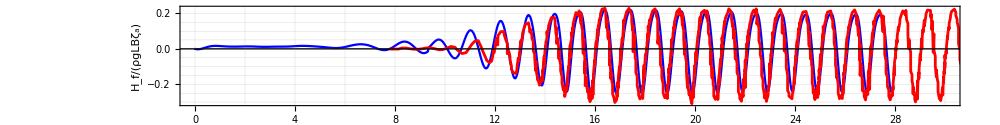

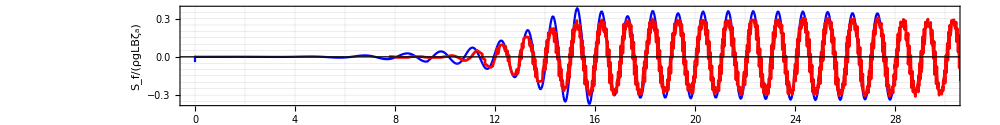

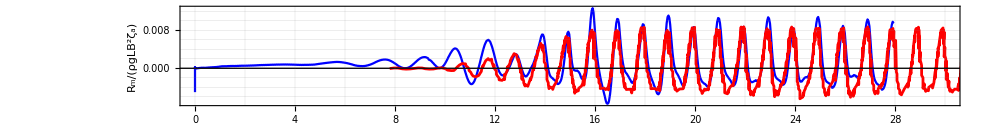

```mathematica
ListPlot[
Append[Table[{importGetData[json,"simulation_time"]/Tw,((importGetData[json,"float_force",i]-importGetData[json,"float_force",i][[5]])/(ρ*g*L*B*ζa))}ᵀ,{i,3,3,1}],
SimuHf],
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["H_f/(ρgLBζ_a)",FontSize->20,FontFamily->"Times"]},
PlotLegends->{"x","y","z"},
Evaluate[plot2Doption]
]

ListPlot[
Append[Table[{importGetData[json,"simulation_time"]/Tw,((importGetData[json,"float_force",i]-importGetData[json,"float_force",i][[5]])/(ρ*g*L*B*ζa))}ᵀ,{i,1,1,1}],
SimuSf],
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["S_f/(ρgLBζ_a)",FontSize->20,FontFamily->"Times"]},
PlotLegends->{"x","y","z"},
Evaluate[plot2Doption]
]

ListPlot[
Append[Table[{importGetData[json,"simulation_time"]/Tw,-((importGetData[json,"float_torque",i]-importGetData[json,"float_torque",i][[15]])/(ρ*g*L*B*B*ζa))}ᵀ,{i,2,2,1}],
SimuRm],
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["R_m/(ρgLB^2ζ_a)",FontSize->20,FontFamily->"Times"]},
PlotLegends->{"x","y","z"},
Evaluate[plot2Doption]
]
```

浮体が流体から受ける，鉛直水平方向の力，y軸回転方向のトルクは，Tanizawa1997の結果とよく一致している．

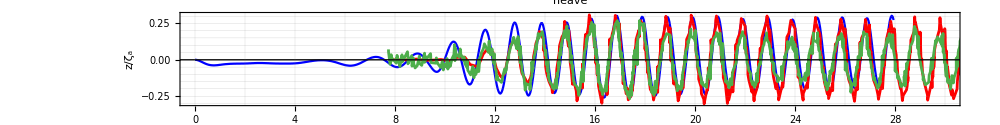

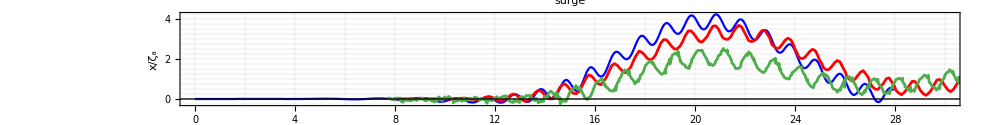

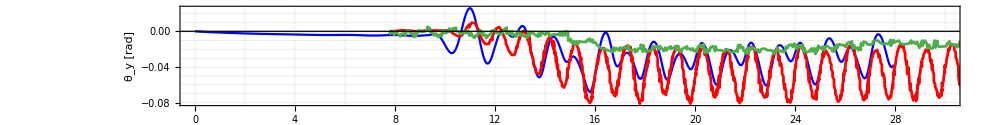

```mathematica
ListPlot[
{{importGetData[json,"simulation_time"]/Tw,(importGetData[json,"float_COM",3]-importGetData[json,"float_COM",3][[1]])/ζa}ᵀ,
SimuHeave,
ExpHeave},
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["z/ζ_a",FontSize->20,FontFamily->"Times"]},
PlotLabel->"heave",
Evaluate[plot2Doption]
]

ListPlot[
{{importGetData[json,"simulation_time"]/Tw,(importGetData[json,"float_COM",1]-importGetData[json,"float_COM",1][[1]])/ζa}ᵀ,
SimuSway,
ExpSway},
Evaluate[opt],
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/ζ_a",FontSize->20,FontFamily->"Times"]},
PlotLabel->"surge",
Evaluate[plot2Doption]
]

k=2π/λ;
ListPlot[
{{importGetData[json,"simulation_time"]/Tw,-10(importGetData[json,"float_pitch"])}ᵀ,
SimuRoll,
ExpRoll},
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["θ_y [rad]",FontSize->20,FontFamily->"Times"]},
Evaluate[plot2Doption]
]
```

ロール角を除き，浮体の並進移動は，Tanizawa1997の計算結果とよく一致している．一方の回転角度は，谷澤の結果よりも小さく

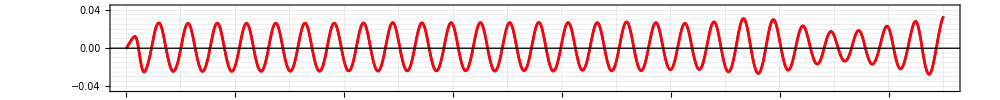
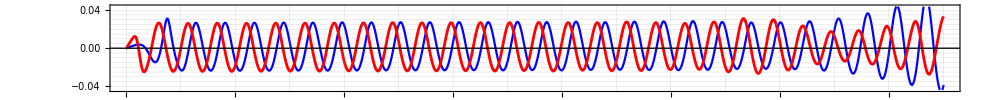
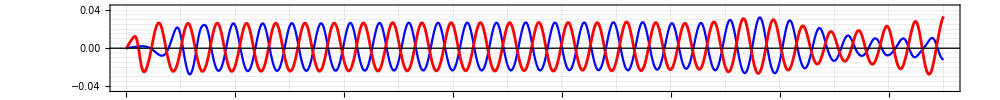
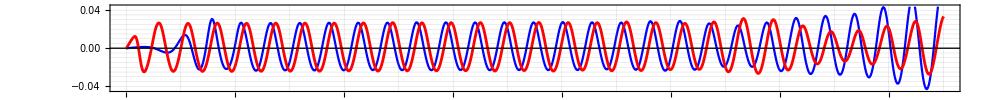
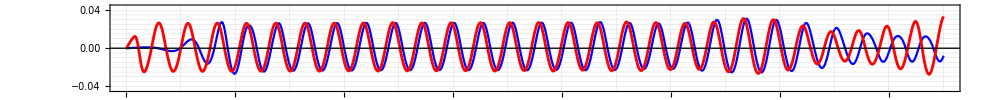
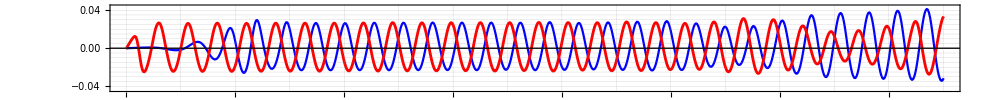
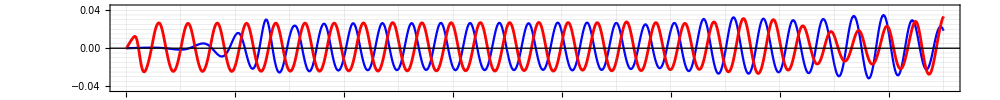
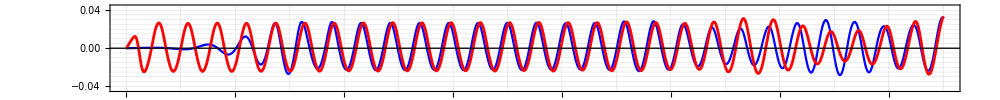
-Graphics-0.2
-Graphics-0.7
-Graphics-1.2
-Graphics-1.7
-Graphics-2.2
-Graphics-2.7
-Graphics-3.2
-Graphics-3.7
-Graphics-4.2
-Graphics-4.7
-Graphics-5.2
-Graphics-5.7
-Graphics-6.2
-Graphics-6.7
-Graphics-7.2
-Graphics-7.7
-Graphics-8.2
-Graphics-8.7
-Graphics-9.2
-Graphics-9.7

```mathematica
delt=0.67/(ω/k);
T=1.;
DATA1=importGetData[json,"gauge0_intersection",3];
Column[ParallelTable[
Module[{data,DATA,position},
data="gauge"<>ToString[i]<>"_intersection";
DATA=importGetData[json,data,3];
position=importGetData[json,data,1][[1]];
Labeled[
ListPlot[
{{importGetData[json,"simulation_time"],(DATA-DATA[[1]])}ᵀ,
{importGetData[json,"simulation_time"](*+(*0.295*)delt*i*),(DATA1-DATA1[[1]])}ᵀ
(*Table[{t,-ζa*Cos[2π/T*t-k*(position)]},{t,0,30,.1}]*)
},
(*FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/H_0",FontSize->20,FontFamily->"Times",Italic]},*)
AspectRatio->1/10,
PlotRange->{Automatic,1.75*{-ζa,ζa}},
Joined->{True,True,True,True,True},
Evaluate[opt],
PlotStyle->plotstyle,
Evaluate[plot2Doption]
]
,position
,Right]
],{i,0,19,1}]
,Spacings->0
]
```

## 収束性のチェック

```mathematica
plotstyle=Table[RGBColor[{Sin[i*π]/2+1/2,Cos[i*π]/2+1/2,i}],{i,0,1,0.2}]
rbgs=Table["#"<>StringJoin[IntegerString[Round[#],16,2]&/@({255*Sin[i*π]/2+1/2,Cos[i*π]/2+1/2,i})],{i,0,1,0.2}]
hexColor="#"<>StringJoin[IntegerString[#,16,2]&/@rbgs[[1]]]


legend={(*"0.1",*)"0.09","0.08","0.07","0.06","0.05"}
```

{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]}

{#000100,#4b0100,#7a0100,#7a0001,#4b0001,#010001}

##000100

{0.09,0.08,0.07,0.06,0.05}

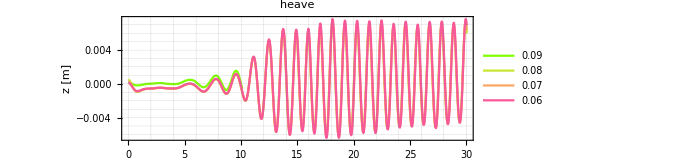

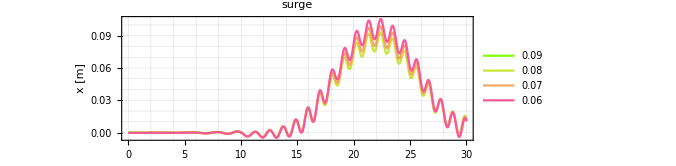

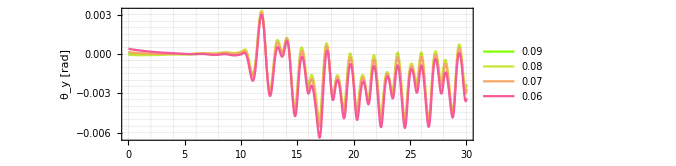

```mathematica
jsons={(*"/Volumes/home/BEM/20240301土木学会東北支部/Tanizawa1996_H0d05_L1d8_potential_water_mod_0d1/result.json",*)
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d08/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d07/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json"(*,
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d05/result.json"*)(*,
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_3/result.json"*)};

plotxrange={{0,30},All};
opt2={FrameStyle->Directive[FontSize->16,Black,Thickness[0.002]],
PlotStyle->plotstyle,
Joined->{True,True,True,True},
PlotRange->plotxrange,
GridLines->All,
GridLinesStyle->Directive[Gray,AbsoluteThickness[0.001]],
ImageSize->500,
(*PlotStyle->{{Darker[Blue,0.1]},{Darker[Blue,0.3]},{Darker[Blue,0.6]},{Darker[Blue,0.9]}},*)
AspectRatio->1/3};
(*メッシュと計算の収束*)

fig=ListPlot[
Table[{importGetData[jsons[[i]],"simulation_time"],(importGetData[jsons[[i]],"float_COM",3]-importGetData[jsons[[i]],"float_COM",3][[150]])}ᵀ,
{i,1,Length[jsons]}],
PlotStyle->plotstyle,
Evaluate[opt2],
(*PlotRange->{{0,12.},{-0.07,0.07}},*)
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["z [m]",FontSize->20,FontFamily->"Times"]},
PlotLegends->legend,
PlotLabel->"heave",
Evaluate[plot2Doption]
]
ListPlot[
Table[{importGetData[jsons[[i]],"simulation_time"],(importGetData[jsons[[i]],"float_COM",1]-importGetData[jsons[[i]],"float_COM",1][[150]])}ᵀ,{i,1,Length[jsons]}],
PlotStyle->plotstyle,
Evaluate[opt2],
PlotRange->{All,Automatic},
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x [m]",FontSize->20,FontFamily->"Times"]},
PlotLegends->legend,
PlotLabel->"surge",
Evaluate[plot2Doption]
]
k=2π/λ;
ListPlot[
Table[{importGetData[jsons[[i]],"simulation_time"],-(importGetData[jsons[[i]],"float_pitch"]-importGetData[jsons[[i]],"float_pitch"][[150]])}ᵀ,{i,1,Length[jsons]}],
PlotStyle->plotstyle,
Evaluate[opt2],
PlotLegends->legend,
PlotRange->{All,All},
PlotRange->{Automatic,Automatic},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["θ_y [rad]",FontSize->20,FontFamily->"Times"]},
Evaluate[plot2Doption]
]
```